```mathematica
<<ProbabilisticBricks`
```

```mathematica
setProblemProperties[11,5,2,1,0.1,0.7];
```

```mathematica
generateContacts[];
```

```mathematica
p=Table[{0,0,1,0,0,0},{nelx}];
p[[IntegerPart[nelx/2]+1]]={0,0,10,15,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

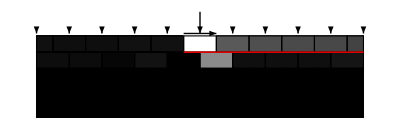

```mathematica
solveProblem[]
displayWallWithFilter["stress_state"]
```

```mathematica
eqCheck
```

True

```mathematica
Hu=Import["collapse_data_10x5.m"];
```

```mathematica
nTests=300;
(*Hu={};*)
For[n=1,n≤nTests,n++,
generateContacts[];
eqCheck=True;
H1=0;H2=15.;f=False;
While[!f,
H=(H1+H2)/2;
p=Table[{0,0,1,0,0,0},{nelx}];
p[[IntegerPart[nelx/2]+1]]={0,0,10,H,0,0};
p=Flatten[p];
setBoundaryConditions[p];
solveProblem[];
If[Abs[H1-H2]<.1,
AppendTo[Hu,H];
f=True;,
If[eqCheck,
H1=H;,
H2=H;
];
];
];
];
Hu;
```

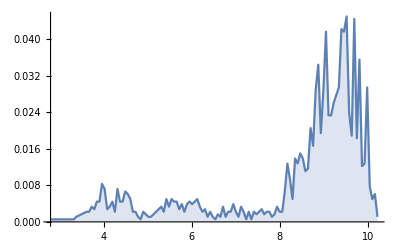

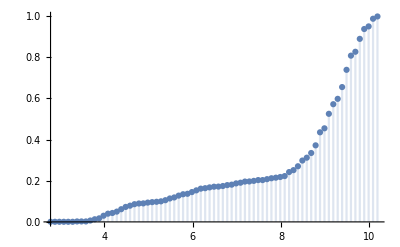

```mathematica
dist=EmpiricalDistribution[Hu];
DiscretePlot[PDF[dist,x],{x,Hu}]
DiscretePlot[CDF[dist,x],{x,Min[Hu],Max[Hu],.1}]
```

```mathematica
{Mean[dist],Quantile[dist,0.05],StandardDeviation[dist],StandardDeviation[dist]/Mean[dist]}
```

{8.39121,4.24805,1.7337,0.206609}

```mathematica
Length[Hu]
```

1800

```mathematica
Export["collapse_data_10x5.m",Hu]
```

collapse_data_10x5.m